```mathematica
SetDirectory[NotebookDirectory[]];
```

## BW fit

### Functions

```mathematica
BW[w_,wr_,Γ_,δbg_,const_,shift_,shift2_]:=
const((Γ/2)^2/((w-wr)^2+(Γ/2)^2))+ δbg((Γ/2)(w-wr))/((w-wr)^2+(Γ/2)^2)+0 ((4 (w-wr)^2- Γ^2) deltabg^2)/(4 (w-wr)^2+Γ^2)+shift (w-wr)+shift2 ;
BWi[w_,wr_,Γ_,const_]:=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)) ;

fit[input_,output_,Tscan_]:=Module[{temp=Range[1,Length[Tscan]],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[n=temp[[ii]];
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];(*maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}],maxxy/30],FindArgMax[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}][[1]]},{a,0,1/2(maxx-minx),1/20}],First][[All,2]]]];*)
maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];
bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[n][[maxxis[[i]]-30,2]]>input[n][[maxxis[[i]],2]],input[n][[maxxis[[i]]+30,2]]>input[n][[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input[n]],maxyi+3(maxyi-hwhmi),Length[input[n]]]};];
If[mins[[1]]≤0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->1000],{i,Length[hwhmi]}];,{ii,Length[Tscan]}];output=temp;];

store[param_,res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=param/.model[[i,ii]]["BestFitParameters"],{ii,Length[res[[i]]]}],{i,Length[res]}];];

storearea[res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=π/2(Γ/.model[[i,ii]]["BestFitParameters"])( const/.model[[i,ii]]["BestFitParameters"]),{ii,Length[res[[i]]]}],{i,Length[res]}];];
```

```mathematica
fitONE[input_]:=Module[{maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxis,mins,hwhmi,bad},
maxx=Max[input[[All,1]]];
minx=Min[input[[All,1]]];
maxy=Max[input[[All,2]]];
maxyx=input[[Position[input,Max[input[[All,2]]]][[1,1]],1]];
maxyi=Position[input[[All,1]],maxyx][[1,1]];
maxxy=input[[Position[input,Max[input[[All,1]]]][[1,1]],2]];
inter=Interpolation[input,InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}],maxxy/30],FindArgMax[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}][[1]]},{a,1,1/2(maxx-minx),1/20}],First][[All,2]]]];bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[[All,1]],Nearest[input[[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[[maxxis[[i]]-30,2]]>input[[maxxis[[i]],2]],input[[maxxis[[i]]+30,2]]>input[[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[[All,2]],Min[input[[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input]]];,
hwhmi=Position[input,Nearest[input[[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input],maxyi+3(maxyi-hwhmi),Length[input]]};];
If[mins[[1]]≤0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input,Nearest[input[[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];];
```

### Fitting

```mathematica
uscanI={1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1};
```

```mathematica
uscanI1={1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10};
```

```mathematica
uscan={1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,99/100};
```

```mathematica
uscan1={1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10};
```

#### Bottomonium Tc Perpendicular

```mathematica
Do[bbdata[n]=Import["bb_perp/swbbu"<>ToString[Round[100uscanI[[n]]]]<>"spectra.dat"];,{n,Length[uscan]}];
```

```mathematica
Do[bbdatau[n]=Import["bb_perp/swbbu"<>ToString[Round[100uscanI[[n]]]]<>"spectrau.dat"];,{n,Length[uscan1]}];
```

```mathematica
Do[bbdatal[n]=Import["bb_perp/swbbu"<>ToString[Round[100uscanI[[n]]]]<>"spectral.dat"];,{n,Length[uscan1]}];
```

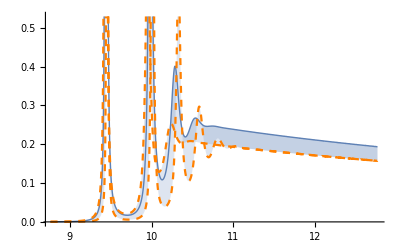

```mathematica
Block[{n=1},ListPlot[{bbdata[n],bbdatal[n],bbdatau[n]},Joined->True,Filling->{1->{2},1->{3}},PlotStyle->{Thick,{Dashed,Orange},{Dashed,Orange}}]]
```

```mathematica
Clear[bbmodelu,bbmodell,bbmodel]
Quiet[fit[bbdata,bbmodel,uscanI]];
Quiet[fit[bbdatal,bbmodell,uscanI1]];
Quiet[fit[bbdatau,bbmodelu,uscanI1]];
```

```mathematica
Clear[wrfitbb,wrfitbbl,wrfitbbu,gfitbb,gfitbbl,gfitbbu,areafitbb,areafitbbu,areafitbbl,cfitbb,cfitbbl,cfitbbu,dfitbb,dfitbbl,dfitbbu,sfitbb,sfitbbl,sfitbbu,s2fitbb,s2fitbbl,s2fitbbu];
store[wr,wrfitbb,bbmodel];
store[wr,wrfitbbl,bbmodell];
store[wr,wrfitbbu,bbmodelu];
store[Γ,gfitbb,bbmodel];
store[Γ,gfitbbl,bbmodell];
store[Γ,gfitbbu,bbmodelu];
store[const,cfitbb,bbmodel];
store[const,cfitbbl,bbmodell];
store[const,cfitbbu,bbmodelu];
store[δbg,dfitbb,bbmodel];
store[δbg,dfitbbl,bbmodell];
store[δbg,dfitbbu,bbmodelu];
store[shift,sfitbb,bbmodel];
store[shift,sfitbbl,bbmodell];
store[shift,sfitbbu,bbmodelu];
store[shift2,s2fitbb,bbmodel];
store[shift2,s2fitbbl,bbmodell];
store[shift2,s2fitbbu,bbmodelu];
storearea[areafitbb,bbmodel];
storearea[areafitbbl,bbmodell];
storearea[areafitbbu,bbmodelu];
```

```mathematica
Append[Transpose[{uscan1,wrfitbb[[;;9,1]],wrfitbbu[[All,1]],wrfitbbl[[All,1]]}],{uscan[[10]],wrfitbb[[10,1]]}]
```

{{1/10,9.44454,9.4373,9.456},{1/5,9.44474,9.43752,9.45614},{3/10,9.44506,9.43787,9.45638},{2/5,9.44551,9.43834,9.45671},{1/2,9.44606,9.43887,9.45714},{3/5,9.44666,9.43938,9.45764},{7/10,9.4472,9.43963,9.45819},{4/5,9.44732,9.43899,9.45866},{9/10,9.44551,9.4348,9.45844},{99/100,9.42354}}

```mathematica
Append[Transpose[{uscan1,wrfitbb[[;;9,2]],wrfitbbu[[All,2]],wrfitbbl[[All,2]]}],{uscan[[10]],wrfitbb[[10,2]]}]
```

{{1/10,9.98253,9.94938,10.009},{1/5,9.98247,9.94921,10.009},{3/10,9.98237,9.94889,10.0091},{2/5,9.98215,9.94834,10.0091},{1/2,9.98176,9.94749,10.0091},{3/5,9.98104,9.94602,10.009},{7/10,9.97964,9.94358,10.0087},{4/5,9.97673,9.93896,10.0076},{9/10,9.96934,9.92858,10.0043},{99/100,9.93859}}

```mathematica
Append[Transpose[{uscan1,wrfitbb[[;;9,3]],wrfitbbu[[All,3]],wrfitbbl[[All,3]]}],{uscan[[10]],wrfitbb[[10,3]]}]
```

{{1/10,10.2762,10.214,10.3268},{1/5,10.276,10.2135,10.3267},{3/10,10.2791,10.2128,10.3265},{2/5,10.2743,10.2126,10.3262},{1/2,10.2733,10.2124,10.3257},{3/5,10.2753,10.2096,10.3248},{7/10,10.2688,10.2074,10.3234},{4/5,10.2634,10.2025,10.3206},{9/10,10.2534,10.194,10.314},{99/100,10.2322}}

```mathematica
(*ListPlot[{Transpose[{uscan[[;;]],wrfitbb1[[;;,2]]}],Transpose[{uscan[[;;]],wrfitbb1[[;;,3]]}],Transpose[{uscan[[;;]],wrfitbb1[[;;,4]]}],Transpose[{uscan[[;;]],wrfitbb2[[;;,2]]}],Transpose[{uscan[[;;]],wrfitbb2[[;;,3]]}],Transpose[{uscan[[;;]],wrfitbb2[[;;,4]]}],Transpose[{uscan[[;;]],wrfitbb3[[;;,2]]}],Transpose[{uscan[[;;]],wrfitbb3[[;;,3]]}],Transpose[{uscan[[;;]],wrfitbb3[[;;,4]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True,AxesLabel->{Style["u",25,Black],Style["M [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["Υ(1S)",25,"Helvetica"],None,None,Style["Υ(2S)",25,"Helvetica"],None,None,Style["Υ(3S)",25,"Helvetica"]}],{0.8,0.4}]]
```

```mathematica
Append[Transpose[{uscan1,gfitbb[[;;9,1]],gfitbbu[[All,1]],gfitbbl[[All,1]]}],{uscan[[10]],gfitbb[[10,1]]}]
```

{{1/10,0.00735038,0.0112024,0.00310006},{1/5,0.00749223,0.011352,0.00316015},{3/10,0.007916,0.0116047,0.00335339},{2/5,0.0080747,0.0119574,0.00338238},{1/2,0.00848569,0.0124487,0.00357973},{3/5,0.0091214,0.01299,0.0038593},{7/10,0.0100263,0.013608,0.00426446},{4/5,0.0113724,0.014316,0.00488819},{9/10,0.0135334,0.0145708,0.005928},{99/100,0.0147324}}

```mathematica
Append[Transpose[{uscan1,gfitbb[[;;9,2]],gfitbbu[[All,2]],gfitbbl[[All,2]]}],{uscan[[10]],gfitbb[[10,2]]}]
```

{{1/10,0.0471611,0.0672473,0.0213498},{1/5,0.0477011,0.0678711,0.0215757},{3/10,0.0488109,0.0688551,0.0221693},{2/5,0.0500945,0.0702827,0.0224186},{1/2,0.051566,0.0720571,0.0230747},{3/5,0.053608,0.0740868,0.0239398},{7/10,0.0561872,0.0760432,0.025021},{4/5,0.0592728,0.0781646,0.0263087},{9/10,0.0622194,0.0765677,0.027458},{99/100,0.0492163}}

```mathematica
Append[Transpose[{uscan1,gfitbb[[;;9,3]],gfitbbu[[All,3]],gfitbbl[[All,3]]}],{uscan[[10]],gfitbb[[10,3]]}]
```

{{1/10,0.115261,0.149561,0.0606799},{1/5,0.116217,0.150715,0.0610538},{3/10,0.112596,0.151954,0.0619796},{2/5,0.120518,0.154489,0.0627317},{1/2,0.122698,0.155533,0.0638202},{3/5,0.120513,0.160142,0.0651597},{7/10,0.129408,0.163027,0.0666093},{4/5,0.132189,0.165282,0.0678339},{9/10,0.132501,0.162783,0.0674592},{99/100,0.0972556}}

```mathematica
(*ListPlot[{Transpose[{uscan[[;;]],gfitbb1[[;;,2]]}],Transpose[{uscan[[;;]],gfitbb1[[;;,3]]}],Transpose[{uscan[[;;]],gfitbb1[[;;,4]]}],Transpose[{uscan[[;;]],gfitbb2[[;;,2]]}],Transpose[{uscan[[;;]],gfitbb2[[;;,3]]}],Transpose[{uscan[[;;]],gfitbb2[[;;,4]]}],Transpose[{uscan[[;;]],gfitbb3[[;;,2]]}],Transpose[{uscan[[;;]],gfitbb3[[;;,3]]}],Transpose[{uscan[[;;]],gfitbb3[[;;,4]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True,AxesLabel->{Style["u",25,Black],Style["Γ [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["Υ(1S)",25,"Helvetica"],None,None,Style["Υ(2S)",25,"Helvetica"],None,None,Style["Υ(3S)",25,"Helvetica"]}],{0.8,0.4}]]
```

#### Charmonium 250 MeV Perpendicular

```mathematica
Do[ccdata[n]=Import["cc_perp/swccu"<>ToString[Round[100uscanI[[n]]]]<>"spectraT250.dat"];,{n,Length[uscan]}];
```

```mathematica
Do[ccdatau[n]=Import["cc_perp/swccu"<>ToString[Round[100uscanI[[n]]]]<>"spectraT250u.dat"];,{n,Length[uscan1]}];
```

```mathematica
Do[ccdatal[n]=Import["cc_perp/swccu"<>ToString[Round[100uscanI[[n]]]]<>"spectraT250l.dat"];,{n,Length[uscan1]}];
```

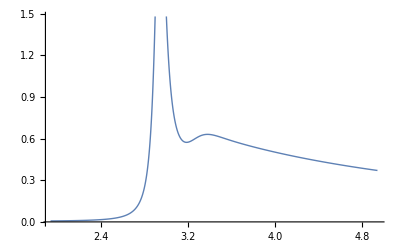

```mathematica
Block[{n=1},ListPlot[{ccdata[n]},Joined->True,PlotStyle->{Thick,{Dashed,Orange},{Dashed,Orange}}]]
```

```mathematica
Clear[ccmodelu,ccmodell,ccmodel]
Quiet[fit[ccdata,ccmodel,uscanI]];
Quiet[fit[ccdatal,ccmodell,uscanI1]];
Quiet[fit[ccdatau,ccmodelu,uscanI1]];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,308.172,0.,0.,0.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,308.172,0.,0.,0.}.

Power::infy: Infinite expression 1/0. encountered.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,308.172,0.,0.,0.}.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,308.172,0.,0.,0.}.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,454.462,0.,0.,0.}.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

NonlinearModelFit::conv: Interior point method fails to converge.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,413.145,0.,0.,0.}.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,454.462,0.,0.,0.}.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,308.172,0.,0.,0.}.

Power::infy: Infinite expression 1/0. encountered.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,343.901,0.,0.,0.}.

Power::infy: Infinite expression 1/0. encountered.

NonlinearModelFit::conv: Interior point method fails to converge.

Power::infy: Infinite expression 1/0. encountered.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,413.145,0.,0.,0.}.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,454.462,0.,0.,0.}.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,413.145,0.,0.,0.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

Power::infy: Infinite expression 1/0. encountered.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,283.549,0.,0.,0.}.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,343.901,0.,0.,0.}.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,413.145,0.,0.,0.}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,454.462,0.,0.,0.}.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,343.901,0.,0.,0.}.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,320.055,0.,0.,0.}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,343.901,0.,0.,0.}.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,374.72,0.,0.,0.}.

NonlinearModelFit::conv: Interior point method fails to converge.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,454.462,0.,0.,0.}.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,466.923,0.,0.,0.}.

General::stop: Further output of Power::infy will be suppressed during this calculation.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,283.549,0.,0.,0.}.

NonlinearModelFit::conv: Interior point method fails to converge.

Power::infy: Infinite expression 1/0. encountered.

NonlinearModelFit::conv: Interior point method fails to converge.

Power::infy: Infinite expression 1/0. encountered.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,413.145,0.,0.,0.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

Power::infy: Infinite expression 1/0. encountered.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,283.549,0.,0.,0.}.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,308.172,0.,0.,0.}.

General::stop: Further output of Power::infy will be suppressed during this calculation.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

General::stop: Further output of IPOPTMinimize::badobj will be suppressed during this calculation.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,283.549,0.,0.,0.}.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,320.055,0.,0.,0.}.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,343.901,0.,0.,0.}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,374.72,0.,0.,0.}.

NonlinearModelFit::conv: Interior point method fails to converge.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,454.462,0.,0.,0.}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,466.923,0.,0.,0.}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::conv: Interior point method fails to converge.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,374.72,0.,0.,0.}.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,413.145,0.,0.,0.}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,466.923,0.,0.,0.}.

NonlinearModelFit::conv: Interior point method fails to converge.

General::stop: Further output of IPOPTMinimize::badobj will be suppressed during this calculation.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,374.72,0.,0.,0.}.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,466.923,0.,0.,0.}.

NonlinearModelFit::conv: Interior point method fails to converge.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,320.055,0.,0.,0.}.

NonlinearModelFit::conv: Interior point method fails to converge.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

General::stop: Further output of NonlinearModelFit::conv will be suppressed during this calculation.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,283.549,0.,0.,0.}.

General::stop: Further output of NonlinearModelFit::conv will be suppressed during this calculation.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,343.901,0.,0.,0.}.

NonlinearModelFit::conv: Interior point method fails to converge.

General::stop: Further output of IPOPTMinimize::badobj will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,320.055,0.,0.,0.}.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,374.72,0.,0.,0.}.

General::stop: Further output of NonlinearModelFit::conv will be suppressed during this calculation.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,466.923,0.,0.,0.}.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,283.549,0.,0.,0.}.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,320.055,0.,0.,0.}.

General::stop: Further output of IPOPTMinimize::badobj will be suppressed during this calculation.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

General::stop: Further output of NonlinearModelFit::conv will be suppressed during this calculation.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,374.72,0.,0.,0.}.

General::stop: Further output of IPOPTMinimize::badobj will be suppressed during this calculation.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,320.055,0.,0.,0.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

General::stop: Further output of NonlinearModelFit::conv will be suppressed during this calculation.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

General::stop: Further output of IPOPTMinimize::badobj will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

General::stop: Further output of NonlinearModelFit::conv will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,466.923,0.,0.,0.}.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

General::stop: Further output of IPOPTMinimize::badobj will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

General::stop: Further output of NonlinearModelFit::conv will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,291.531,0.,0.,0.}.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,291.531,0.,0.,0.}.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,281.578,0.,0.,0.}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,291.531,0.,0.,0.}.

Power::infy: Infinite expression 1/0. encountered.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,348.3,0.,0.,0.}.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,291.531,0.,0.,0.}.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

Power::infy: Infinite expression 1/0. encountered.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,333.067,0.,0.,0.}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,308.145,0.,0.,0.}.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,327.75,0.,0.,0.}.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,281.578,0.,0.,0.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,348.3,0.,0.,0.}.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,361.935,0.,0.,0.}.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,281.578,0.,0.,0.}.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,291.531,0.,0.,0.}.

Power::infy: Infinite expression 1/0. encountered.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,348.3,0.,0.,0.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,333.067,0.,0.,0.}.

Power::infy: Infinite expression 1/0. encountered.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,281.578,0.,0.,0.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,348.3,0.,0.,0.}.

Power::infy: Infinite expression 1/0. encountered.

NonlinearModelFit::conv: Interior point method fails to converge.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,308.145,0.,0.,0.}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,327.75,0.,0.,0.}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,308.145,0.,0.,0.}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,327.75,0.,0.,0.}.

NonlinearModelFit::conv: Interior point method fails to converge.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,361.935,0.,0.,0.}.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,333.067,0.,0.,0.}.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,263.838,0.,0.,0.}.

NonlinearModelFit::conv: Interior point method fails to converge.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,308.145,0.,0.,0.}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,327.75,0.,0.,0.}.

NonlinearModelFit::conv: Interior point method fails to converge.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,281.578,0.,0.,0.}.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,291.531,0.,0.,0.}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,348.3,0.,0.,0.}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,333.067,0.,0.,0.}.

Power::infy: Infinite expression 1/0. encountered.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,361.935,0.,0.,0.}.

NonlinearModelFit::conv: Interior point method fails to converge.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::conv: Interior point method fails to converge.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,333.067,0.,0.,0.}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,263.838,0.,0.,0.}.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,281.578,0.,0.,0.}.

General::stop: Further output of IPOPTMinimize::badobj will be suppressed during this calculation.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,308.145,0.,0.,0.}.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,327.75,0.,0.,0.}.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,348.3,0.,0.,0.}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,361.935,0.,0.,0.}.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,263.838,0.,0.,0.}.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,263.838,0.,0.,0.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

General::stop: Further output of NonlinearModelFit::conv will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,361.935,0.,0.,0.}.

General::stop: Further output of IPOPTMinimize::badobj will be suppressed during this calculation.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

General::stop: Further output of IPOPTMinimize::badobj will be suppressed during this calculation.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,308.145,0.,0.,0.}.

General::stop: Further output of IPOPTMinimize::badobj will be suppressed during this calculation.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,333.067,0.,0.,0.}.

NonlinearModelFit::conv: Interior point method fails to converge.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

General::stop: Further output of NonlinearModelFit::conv will be suppressed during this calculation.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::conv: Interior point method fails to converge.

General::stop: Further output of NonlinearModelFit::conv will be suppressed during this calculation.

General::stop: Further output of IPOPTMinimize::badobj will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,263.838,0.,0.,0.}.

General::stop: Further output of IPOPTMinimize::badobj will be suppressed during this calculation.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,327.75,0.,0.,0.}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,361.935,0.,0.,0.}.

General::stop: Further output of NonlinearModelFit::conv will be suppressed during this calculation.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::conv: Interior point method fails to converge.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

General::stop: Further output of NonlinearModelFit::conv will be suppressed during this calculation.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::conv: Interior point method fails to converge.

General::stop: Further output of IPOPTMinimize::badobj will be suppressed during this calculation.

General::stop: Further output of NonlinearModelFit::conv will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

General::stop: Further output of NonlinearModelFit::conv will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,263.838,0.,0.,0.}.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

General::stop: Further output of IPOPTMinimize::badobj will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

General::stop: Further output of NonlinearModelFit::conv will be suppressed during this calculation.

```mathematica
Clear[wrfitcc,wrfitccl,wrfitccu,gfitcc,gfitccl,gfitccu,areafitcc,areafitccu,areafitccl,cfitcc,cfitccl,cfitccu,dfitcc,dfitccl,dfitccu,sfitcc,sfitccl,sfitccu,s2fitcc,s2fitccl,s2fitccu];
store[wr,wrfitcc,ccmodel];
store[wr,wrfitccl,ccmodell];
store[wr,wrfitccu,ccmodelu];
store[Γ,gfitcc,ccmodel];
store[Γ,gfitccl,ccmodell];
store[Γ,gfitccu,ccmodelu];
store[const,cfitcc,ccmodel];
store[const,cfitccl,ccmodell];
store[const,cfitccu,ccmodelu];
store[δbg,dfitcc,ccmodel];
store[δbg,dfitccl,ccmodell];
store[δbg,dfitccu,ccmodelu];
store[shift,sfitcc,ccmodel];
store[shift,sfitccl,ccmodell];
store[shift,sfitccu,ccmodelu];
store[shift2,s2fitcc,ccmodel];
store[shift2,s2fitccl,ccmodell];
store[shift2,s2fitccu,ccmodelu];
storearea[areafitcc,ccmodel];
storearea[areafitccl,ccmodell];
storearea[areafitccu,ccmodelu];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,283.549,0.,0.,0.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,283.549,0.,0.,0.}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,290.477,0.,0.,0.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::conv: Interior point method fails to converge.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,308.172,0.,0.,0.}.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

General::stop: Further output of IPOPTMinimize::badobj will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

General::stop: Further output of NonlinearModelFit::conv will be suppressed during this calculation.

$Aborted

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,263.838,0.,0.,0.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,263.838,0.,0.,0.}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::conv: Interior point method fails to converge.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {wr,Γ,const,δbg,shift,shift2} = {1.93838,0.,269.086,0.,0.,0.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

```mathematica
Append[Transpose[{uscan1,wrfitcc[[;;9,1]],wrfitccu[[All,1]],wrfitccl[[All,1]]}],{uscan[[10]],wrfitcc[[10,1]]}]
```

```mathematica
Append[Transpose[{uscan1,wrfitcc[[;;9,2]],wrfitccu[[All,2]],wrfitccl[[All,2]]}],{uscan[[10]],wrfitcc[[10,2]]}]
```

```mathematica
Append[Transpose[{uscan1,gfitcc[[;;9,1]],gfitccu[[All,1]],gfitccl[[All,1]]}],{uscan[[10]],gfitcc[[10,1]]}]
```

```mathematica
Append[Transpose[{uscan1,gfitcc[[;;9,2]],gfitccu[[All,2]],gfitccl[[All,2]]}],{uscan[[10]],gfitcc[[10,2]]}]
```

```mathematica
(*gfit250cc1=gfit250cc10/.{a_,b_,c_,d_}:>{a,b,c,b-(c-b)}*)
```

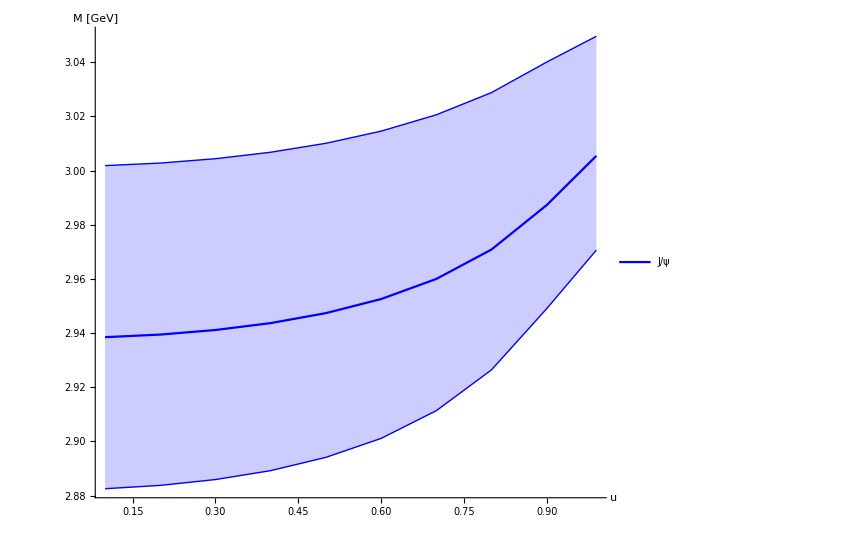

```mathematica
(*ListPlot[{Transpose[{uscan[[;;]],wrfit250cc1[[;;,2]]}],Transpose[{uscan[[;;]],wrfit250cc1[[;;,3]]}],Transpose[{uscan[[;;]],wrfit250cc1[[;;,4]]}]},PlotRange->All,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True,AxesLabel->{Style["u",25,Black],Style["M [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["J/ψ",25,"Helvetica"]}],{0.8,0.2}]]
```

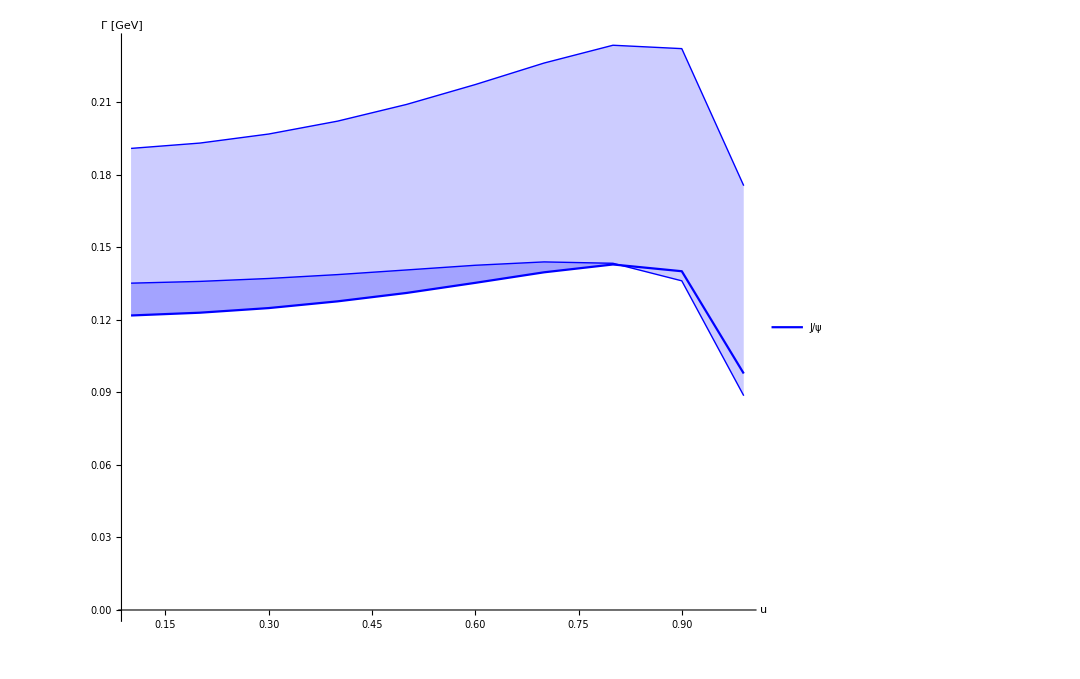

```mathematica
(*ListPlot[{Transpose[{uscan[[;;]],gfit250cc10[[;;,2]]}],Transpose[{uscan[[;;]],gfit250cc10[[;;,3]]}],Transpose[{uscan[[;;]],gfit250cc10[[;;,4]]}]},PlotRange->All,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True,AxesLabel->{Style["u",25,Black],Style["Γ [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["J/ψ",25,"Helvetica"]}],{0.8,0.2}]]
```

#### Bottomonium 250 MeV Perpendicular

```mathematica
Do[bbdata2[n]=Import["bb_perp/swbbu"<>ToString[Round[100uscanI[[n]]]]<>"spectraT250.dat"];,{n,Length[uscan]}];
```

```mathematica
Do[bbdata2u[n]=Import["bb_perp/swbbu"<>ToString[Round[100uscanI[[n]]]]<>"spectraT250u.dat"];,{n,Length[uscan1]}];
```

```mathematica
Do[bbdata2l[n]=Import["bb_perp/swbbu"<>ToString[Round[100uscanI[[n]]]]<>"spectraT250l.dat"];,{n,Length[uscan1]}];
```

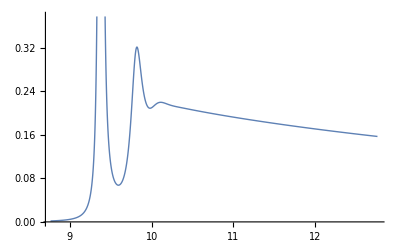

```mathematica
Block[{n=9},ListPlot[{bbdata2[n]},Joined->True,PlotStyle->{Thick,{Dashed,Orange},{Dashed,Orange}}]]
```

```mathematica
Clear[bbmodelu,bbmodell,bbmodel]
Quiet[fit[bbdata2,bbmodel,uscanI]];
```

```mathematica
Clear[wrfitbb,wrfitbbl,wrfitbbu,gfitbb,gfitbbl,gfitbbu,areafitbb,areafitbbu,areafitbbl,cfitbb,cfitbbl,cfitbbu,dfitbb,dfitbbl,dfitbbu,sfitbb,sfitbbl,sfitbbu,s2fitbb,s2fitbbl,s2fitbbu];
store[wr,wrfitbb,bbmodel];
store[Γ,gfitbb,bbmodel];
store[const,cfitbb,bbmodel];
store[δbg,dfitbb,bbmodel];
store[shift,sfitbb,bbmodel];
store[shift2,s2fitbb,bbmodel];
storearea[areafitbb,bbmodel];
```

```mathematica
Transpose[{uscan,wrfitcc[[All,1]]}]
```

```mathematica
Transpose[{uscan,gfitcc[[All,1]]}]
```

```mathematica
NotebookSave[];
```